### Full Generality

```mathematica
α = ({{α1}, {α2}, {α3}});
c0=({{0}, {d}, {1}});
c1=({{0}, {d}, {1}});
β1=({{β11}, {β12}, {β13}});
β2=({{β21}, {β22}, {β23}});
A0=({{0, 0, 0}, {γ, γ, 0}, {a, b, γ}}); (* A0=({{A011, A012, A013}, {A021, A022, A023}, {A031, A032, A033}}); *)
B0=({{0, 0, 0}, {B021, 0, 0}, {B031, B032, 0}}); (* Subscript[B, 0]=({{B011, B012, B013}, {B021, B022, B023}, {B031, B032, B033}}); *)
H0=({{H01}, {H02}, {H03}});
VU=({{U}, {U}, {U}});
e = ({{1}, {1}, {1}});
```

```mathematica
K1=IdentityMatrix[3] - μ h A0 ;
MatrixForm[K1 ]
```

(1 | 0 | 0
-h γ μ | 1-h γ μ | 0
-a h μ | -b h μ | 1-h γ μ)

```mathematica
K2 = VU + B0 . e  σ (σ I10)/h;
MatrixForm[K2]
```

(U
U+1/2 B021 (W+Z/(√3)) σ^2
U+1/2 (B031+B032) (W+Z/(√3)) σ^2)

```mathematica
H0= Inverse[K1].K2;
MatrixForm[H0]
```

(U
(U (h γ μ-h^2 γ^2 μ^2))/(1-h γ μ)^2+(U+1/2 B021 (W+Z/(√3)) σ^2)/(1-h γ μ)
(U (a h μ-a h^2 γ μ^2+b h^2 γ μ^2))/(1-h γ μ)^2+(b h μ (U+1/2 B021 (W+Z/(√3)) σ^2))/(1-h γ μ)^2+(U+1/2 (B031+B032) (W+Z/(√3)) σ^2)/(1-h γ μ))

```mathematica
U2= U+ μ h αᵀ.H0 + σ I1 Transpose[e].β1+ σ I10/h Transpose[e].β2;
U2 =U2[[1]][[1]];
U2
```

U+W (β11+β12+β13) σ+1/2 (W+Z/(√3)) (β21+β22+β23) σ+h μ (U α1+α2 ((U (h γ μ-h^2 γ^2 μ^2))/(1-h γ μ)^2+(U+1/2 B021 (W+Z/(√3)) σ^2)/(1-h γ μ))+α3 ((U (a h μ-a h^2 γ μ^2+b h^2 γ μ^2))/(1-h γ μ)^2+(b h μ (U+1/2 B021 (W+Z/(√3)) σ^2))/(1-h γ μ)^2+(U+1/2 (B031+B032) (W+Z/(√3)) σ^2)/(1-h γ μ)))

```mathematica
I10=1/2 h(W+Z/(√3)); 
I1= W;
```

```mathematica
U2Full = U2
```

U+W (β11+β12+β13) σ+1/2 (W+Z/(√3)) (β21+β22+β23) σ+h μ (U α1+α2 ((U (h γ μ-h^2 γ^2 μ^2))/(1-h γ μ)^2+(U+1/2 B021 (W+Z/(√3)) σ^2)/(1-h γ μ))+α3 ((U (a h μ-a h^2 γ μ^2+b h^2 γ μ^2))/(1-h γ μ)^2+(b h μ (U+1/2 B021 (W+Z/(√3)) σ^2))/(1-h γ μ)^2+(U+1/2 (B031+B032) (W+Z/(√3)) σ^2)/(1-h γ μ)))

```mathematica
U2Plugged = U2Full /.  {W -> 0,Z->0}
G = Coefficient[U2Plugged,U]
```

U+h μ (U α1+α3 ((b h U μ)/(1-h γ μ)^2+U/(1-h γ μ)+(U (a h μ-a h^2 γ μ^2+b h^2 γ μ^2))/(1-h γ μ)^2)+α2 (U/(1-h γ μ)+(U (h γ μ-h^2 γ^2 μ^2))/(1-h γ μ)^2))

1+h α1 μ+(a h^2 α3 μ^2)/(1-h γ μ)^2+(b h^2 α3 μ^2)/(1-h γ μ)^2+(h^2 α2 γ μ^2)/(1-h γ μ)^2-(a h^3 α3 γ μ^3)/(1-h γ μ)^2+(b h^3 α3 γ μ^3)/(1-h γ μ)^2-(h^3 α2 γ^2 μ^3)/(1-h γ μ)^2+(h α2 μ)/(1-h γ μ)+(h α3 μ)/(1-h γ μ)

```mathematica
stableeq = FullSimplify[G/.  {μ -> z/h}]
```

1+z α1-z α2+(2 b z^2 α3)/(-1+z γ)^2-(z (2 α2+α3+a z α3-b z α3))/(-1+z γ)

```mathematica
Together[stableeq]
```

(1+z α1+z α2+z α3+a z^2 α3+b z^2 α3-2 z γ-2 z^2 α1 γ-z^2 α3 γ-a z^3 α3 γ+b z^3 α3 γ+z^2 γ^2+z^3 α1 γ^2-z^3 α2 γ^2)/(-1+z γ)^2

```mathematica
Limit[stableeq,z-> ∞]
```

DirectedInfinity[α1-α2-(a α3)/γ+(b α3)/γ]

```mathematica
Together[stableeq /. a->b]
```

(1+z α1+z α2+z α3+2 b z^2 α3-2 z γ-2 z^2 α1 γ-z^2 α3 γ+z^2 γ^2+z^3 α1 γ^2-z^3 α2 γ^2)/(-1+z γ)^2

```mathematica
Limit[stableeq /. a->b,z-> ∞]
```

DirectedInfinity[α1-α2]

```mathematica
Limit[stableeq /. {a->b,α1-> α2} ,z-> ∞] /. -2α2-α3->-1
```

(2 b α3+(-1+γ) γ)/γ^2

```mathematica
Solve[2 b α3+(-1+γ) γ==0,γ]
```

{{γ→1/2 (1-√(1-8 b α3))},{γ→1/2 (1+√(1-8 b α3))}}

```mathematica
cond1 = First[First[Transpose[α].e]] == 1;
cond2 = First[First[Transpose[β1].e]] == 1;
cond3 = First[First[Transpose[β2].e]] == 0;
cond4 = First[First[Transpose[α].B0.e]] == 1;
cond5 = First[First[Transpose[α].A0.e]] == 1/2;
cond6 = First[First[Transpose[α].(B0.e)^2]] == 3/2;
cond7 = First[First[Transpose[β1].c1]] == 1;
cond8 = First[First[Transpose[β2].c1]] == -1;
```

```mathematica
conds = {cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8} /. {a->b,α1-> α2,γ->1/2 (1-√(1-8 b α3))}
vars = {a,b,α3,A031,A032,d,β11,β12,β13,β21,β22,β23,B021,B031,B032};
```

{2 b+α3==1,β11+β12+β13==1,β21+β22+β23==0,b B021+B031 α3+B032 α3==1,2 b α3+b (1-√(1-8 b α3))+1/2 α3 (1-√(1-8 b α3))==1/2,b B021^2+(B031+B032)^2 α3==3/2,d β12+β13==1,d β22+β23==-1}

```mathematica
FindInstance[conds,vars]
```

{{a→-23/5-(11 ⅈ)/5,b→1/(2 √2),α3→1/2 (2-√2),A031→33/10+(8 ⅈ)/5,A032→-23/5-(29 ⅈ)/10,d→1,β11→0,β12→2,β13→-1,β21→1,β22→0,β23→-1,B021→1/7 (8+2 √2-ⅈ √(2 (34-23 √2))),B031→-2+(31 ⅈ)/10,B032→1/70 ((220-217 ⅈ)+20 √2+10 ⅈ √(34-23 √2)+5 ⅈ √(2 (34-23 √2)))}}

```mathematica
N[FindInstance[conds,vars,Reals]]
```

{{a→15.1,b→0.146447,α3→0.707107,A031→1.6,A032→2.,d→0.,β11→0.,β12→0.,β13→1.,β21→1.,β22→0.,β23→-1.,B021→-0.191462,B031→0.,B032→1.45387}}

```mathematica
conds = {cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,1>d>0} /. {a->b,α1-> α2,γ->1/2 (1-√(1-8 b α3))}
vars = {a,b,α3,A031,A032,d,β11,β12,β13,β21,β22,β23,B021,B031,B032};
```

{2 b+α3==1,β11+β12+β13==1,β21+β22+β23==0,b B021+B031 α3+B032 α3==1,2 b α3+b (1-√(1-8 b α3))+1/2 α3 (1-√(1-8 b α3))==1/2,b B021^2+(B031+B032)^2 α3==3/2,d β12+β13==1,d β22+β23==-1,1>d>0}

```mathematica
N[FindInstance[conds,vars,Reals]]
```

{{a→15.1,b→0.146447,α3→0.707107,A031→1.6,A032→2.,d→0.5,β11→0.,β12→0.,β13→1.,β21→1.,β22→0.,β23→-1.,B021→-0.191462,B031→0.,B032→1.45387}}

```mathematica
stableeq /. {a->b,α1-> α2,γ->1/2 (1-√(1-8 b α3))} /.{a->15.1,b->0.1464466094067262,α3->0.7071067811865476,A031->1.6,A032->2.,d->0.5,β11->0.,β12->0.,β13->1.,β21->1.,β22->0.,β23->-1.,B021->-0.19146211192335333,B031->0.,B032->1.4538666640927194} /. α2 -> 0.25
```

1-(1.20711 z)/(-1+0.292893 z)+(0.207107 z^2)/(-1+0.292893 z)^2

```mathematica
GG[z_]:=1-(1.2071067811865475 z)/(-1+0.2928932188134524 z)+(0.20710678118654752 z^2)/(-1+0.2928932188134524 z)^2
```

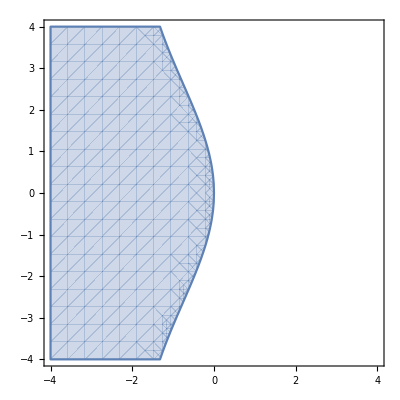

```mathematica
RegionPlot[Abs[GG[x + ⅈ y]]<1,{x,-4,4},{y,-4,4}]
```